```mathematica
f[g_,Ω_]:=NDSolve[{x'[t]==ⅈ*g*Ω(2ⅈ Im[z[t]*y[t]+g*x[t]]),y'[t]==ⅈ*g*Ω(-2ⅈ Im[z[t]*x[t]+g*y[t]]), z'[t]==ⅈ(Ω*z[t]-g*y[t]),x[0]==0,y[0]==Exp[-g^2/2], z[0]==0},{x,y,z},{t,0,50}];
coherent[g_,Ω_, α_]:=NDSolve[{x'[t]==ⅈ*g*Ω(2ⅈ Im[z[t]*y[t]+g*x[t]]),y'[t]==ⅈ*g*Ω(-2ⅈ Im[z[t]*x[t]+g*y[t]]), z'[t]==ⅈ(Ω*z[t]-g*y[t]),x[0]==0,y[0]==Exp[-g^2/2]*Cos[2*g*α], z[0]==0},{x,y,z},{t,0,50}];
```

10

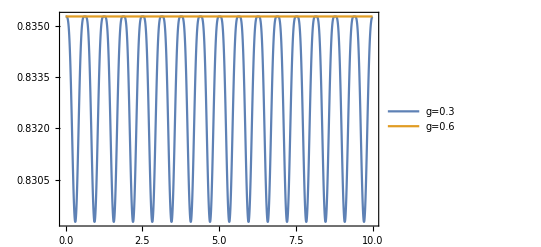

```mathematica
g1=.6;
g2=.6;

g3=1.0;
Omega=10
Plot[{Evaluate[y[t]/.f[g1,Omega]], Exp[-g1^2/2]},{t,0,10} , PlotRange->All, Frame->True, PlotLegends->{"g=0.3", "g=0.6", "g=1.0"}]
```

```mathematica
complete[g_,Ω_,T_,J_]:=NDSolve[{x'[t]==ⅈ*g*Ω(-2ⅈ Im[a[t]*y[t]+g*x[t]]),y'[t]==ⅈ*g*Ω(2ⅈ Im[a[t]*x[t]+g*y[t]]), a'[t]==ⅈ(-Ω*a[t]+g*T*y[t]- g*J*x[t]),x[0]==0,y[0]==Exp[-g^2/2], z[0]==0},{x,y,z},{t,0,50}];
g=1
Omega=10
Plot[{Evaluate[y[t]/.f[g,0.1]],Evaluate[y[t]/.f[g,10]],Evaluate[y[t]/.f[g,25]], Exp[-g^2/2]},{t,0,50} , PlotRange->All, Frame->True]
```

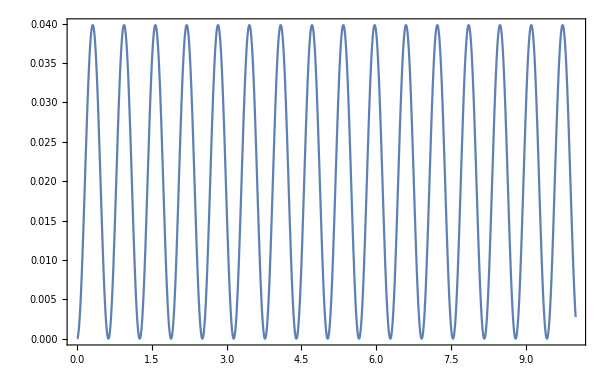

```mathematica
Plot[{Evaluate[2Re[z[t]/.f[0.1,10]]]},{t,0,10} , PlotRange->All, Frame->True, PlotLegends->Automatic]
```

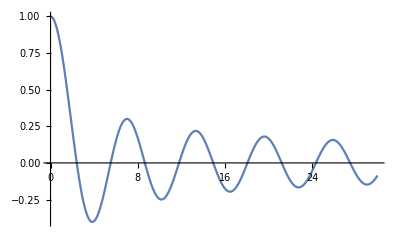

```mathematica
Plot[BesselJ[0, t],{t,0,30}]
```

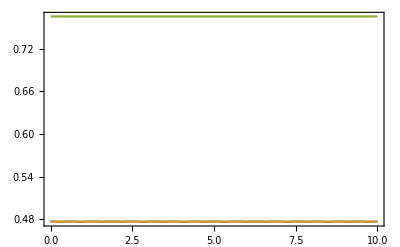

```mathematica
g=0.5;
α=1;
Plot[{Evaluate[y[t]/.coherent[g,Omega, α]], Exp[-g^2/2]*Cos[2*g*α], BesselJ[0, 2*g]},{t,0,10} , PlotRange->All, Frame->True]
```

```mathematica
Integrate[HermiteH[n,x]*Cos[x]*Exp[-x^2/2], x]
```

```mathematica
ψ[n_,x_]:=1/Sqrt[Sqrt[Pi] 2^n n!] Exp[-x^2/2] HermiteH[n,x];
cs0[g_,n_]:=Integrate[ψ[n,x]^2 Cos[√2 g*x],{x,-∞,+∞} ];
SolN[g_,Ω_, n_]:=NDSolve[{x'[t]==ⅈ*g*Ω(2ⅈ Im[z[t]*y[t]+g*x[t]]),y'[t]==ⅈ*g*Ω(-2ⅈ Im[z[t]*x[t]+g*y[t]]), z'[t]==ⅈ(Ω*z[t]-g*y[t]),x[0]==0,y[0]==cs0[g, n], z[0]==0},{x,y,z},{t,0,10}];
```

```mathematica
g=0.5;
Omega=10;
n=10;
```

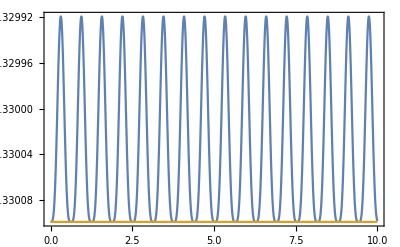

```mathematica
Plot[{Evaluate[y[t]/.SolN[g,Omega, n]], cs0[g,n]},{t,0,10} , PlotRange->All, Frame->True]
```

```mathematica
Plot[cs0[0.5,n],{n,0,10}]
```

NIntegrate::deorela: The relative error 10. is larger than expected for the integrand 0.564176 ⅇ^(-Abs[0.-x]^2) Cos[0.707107 x] HermiteH[0.000204286,-Abs[0.-x]]^2 over {0,∞} with DoubleExponentialOscillatory method and automatic tuning parameters, TuningParameters -> {10,5}. The integration will proceed with TuningParameters -> {1,5}.

General::munfl: Exp[-3.14135×10^10] is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

NIntegrate::deorel: The relative error ComplexInfinity is larger than expected for the integrand 0.564176 ⅇ^(-Abs[0.-x]^2) Cos[0.707107 x] HermiteH[0.000204286,-Abs[0.-x]]^2 over {0,∞} with DoubleExponentialOscillatory method and tuning parameters, TuningParameters -> {1,5}.

NIntegrate::deoncon: DoubleExponentialOscillatory has failed to converge for the integrand 0.564176 ⅇ^(-Abs[0.-x]^2) Cos[0.707107 x] HermiteH[0.000204286,-Abs[0.-x]]^2 over {0,∞}. DoubleExponentialOscillatory obtained 3.68999×10^250 and ComplexInfinity for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-27.0423}. NIntegrate obtained 8.04238251591042×10^310 and 7.73079084184739×10^310 for the integral and error estimates.

$Aborted